```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"]];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

```mathematica
coeff[n_]:=(1+(PDF[FRatioDistribution[1,n],n]/n));
N[coeff[1]]
```

1.15915

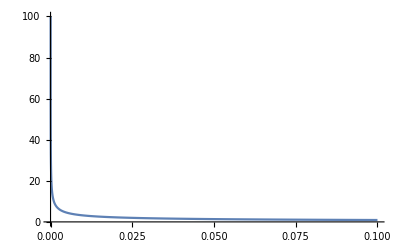

```mathematica
NIntegrate[PDF[FRatioDistribution[1,1],x],{x,0,10}]==.683,{x,0,.1},PlotRange->{{0,.1},{0,100}}]
```

```mathematica
tst[x_]:=Table[Exp[-k x],{k,1,10}];
Integrate[tst[x]Exp[3x],{x,- Pi, Pi}]
```

{Sinh[2 π],-ⅇ^-π+ⅇ^π,2 π,2 Sinh[π],Sinh[2 π],2/3 Sinh[3 π],1/2 Sinh[4 π],2/5 Sinh[5 π],1/3 Sinh[6 π],2/7 Sinh[7 π]}